## Solar Data

```mathematica
build=0;
SetDirectory[NotebookDirectory[]];
SSM=Import["data/agss09.dat"];
k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity in m/s*)
SR=6.9598 10^8;(*Solar radius in m*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
mp=0.938272(*proton mass, GeV*);
SM=1.989 10^30(*Solar mass in kg*);
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)};

(*THIS IS ELEMENTS USED IN FENG*)
atomscut={"He4","N14","O16","Ne","Mg","Si","S","Fe"};

atomscut={"H1","He4","N14","O16","Ne","Mg","Si","S","Fe"};


Fiinf={{"He4",0.986},{"N14",0.613},{"O16",0.613},{"Mg",0.281},{"Si",0.281},{"Fe",0.00677}};
mic={{"He4",18.2},{"N14",75.2},{"O16",75.2},{"Mg",71.7},{"Si",71.7},{"Fe",29.3}};
αi={{"He4",1.58},{"N14",2.69},{"O16",2.69},{"Mg",2.97},{"Si",2.97},{"Fe",3.36}};
(*FULL LIST OF ELEMENTS*)
atomscut={"H1","He4","He3","C12","C13","N14","N15","O16","O17","O18","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};

(*My list of elements*)
atomscut={"H1","He4","C12","N14","O16","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};


(*Full list of elements: {Name, atomic weight in a.u., number of protons}*)
mNuF={{"H1",1.007825,1},{"He4",4.002603,2},{"He3",3.0160293,2},{"C12",12.,6},{"C13",13.00335483521,6},{"N14",14.00307400446,7},{"N15",15.0001088989,7},{"O16",15.99491461960,8},{"O17",16.9991317566,8},{"O18",17.9991596128,8},{"Ne",20.1797,10},{"Na",22.98976928,11},{"Mg",24.305,12},{"Al",26.9815385,13},{"Si",28.085,14},{"P",30.973761998,15},{"S",32.06,16},{"Cl",35.45,17},{"Ar",39.948,18},{"K",39.0983,19},{"Ca",40.078,20},{"Sc",44.955908,21},{"Ti",47.867,22},{"V",50.9415,23},{"Cr",51.9961,24},{"Mn",54.938043,25},{"Fe",55.845,26},{"Co",58.933194,27},{"Ni",58.6934,28}};
(*element mass functions: {Name, mass [r (m)] (kg) *)
elemfF={};
Do[
elemfF=Append[elemfF,Interpolation[Table[{SSM⟦i,2⟧*SR,SSM⟦i,j⟧},{i,2,Length[SSM]}]]],{j,7,Length[SSM⟦1⟧]}];
(*ndfF is number density function {Name, density [r (m)] (m^-3)}*)
ndfF={};
Do[
ndfF=Append[ndfF,{SSM⟦1,j⟧,Interpolation[Table[{SSM⟦i,2⟧*SR,(SSM⟦i,j⟧(*mass fraction*)*SSM⟦i,4⟧*0.001*100^3(*density (kg/m^3)*))/(mNuF⟦j-6,2⟧*1.660539 10^-27(*kg/u*))},{i,2,Length[SSM]}]]}],{j,7,Length[SSM⟦1⟧]}];
fiF={};
Do[
fiF=Append[fiF,{SSM⟦1,j⟧,NIntegrate[4π r^2 ndfF⟦j-6,2⟧[r],{r,0,SR},WorkingPrecision-> 7]/tn}],{j,7,Length[SSM⟦1⟧]}];


(*an is atomic number of nuclei = mass in au*)
An={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],An=Append[An,mNuF⟦i,2⟧]],{i,1,Length[mNuF]}];
(*mn is mass of nuclei in GeV*)
mn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],mn=Append[mn,mNuF⟦i,2⟧*0.9314941(*GeV/au*)]],{i,1,Length[mNuF]}];
(*zn is number of protons in each atom*)
zn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],zn=Append[zn,mNuF⟦i,3⟧]],{i,1,Length[mNuF]}];
(*ndf is number density function [r (m)], m^-3*)
ndf={};
Do[If[MemberQ[atomscut,ndfF⟦i,1⟧],ndf=Append[ndf,ndfF⟦i,2⟧]],{i,1,Length[mNuF]}];
fi={};
Do[If[MemberQ[atomscut,fiF⟦i,1⟧],fi=Append[fi,fiF⟦i,2⟧]],{i,1,Length[mNuF]}];

(*Table[{atomscut⟦i⟧,Log10[NIntegrate[4π r^2 ndf⟦i⟧[r],{r,0,SR}]/(tn*0.92)]+12},{i,1,Length[ndf]}]*)
```

## MicrOmegas

```mathematica
microrun[aDM_,MDVB_,MXd_,gSM_]:=(
$micropath="/home/isanderson/src/physics/micromegas_5.0.8/SMDP";
$microout="microout";
$paramsfile="paramsfile.par";
SetDirectory[$micropath];
params={{"aDM",aDM},{"MDVB",MDVB},{"MXd",MXd},{"gSM",gSM}};
Export[$paramsfile,params,"Table"];
Run["./main "<>$paramsfile<>" > "<>$microout];
str=OpenRead[$microout];
capline = Find[str,"Capture Rate is"];
capstring=StringTake[capline,-13];
capstring=StringReplace[capstring,"E+"-> "*10^"];
capstring=StringReplace[capstring,"E-"-> "*10^-"];
caprate=ToExpression[capstring];

crosspbline=Find[str,"proton  SI"];
crosspbstring=StringTake[crosspbline,{13,21}];
crosspbstring=StringReplace[crosspbstring,"E+"-> "*10^"];
crosspbstring=StringReplace[crosspbstring,"E-"-> "*10^-"];
crosspb=ToExpression[crosspbstring];
crossm2=crosspb*10^-36(*pb to cm^2*)*10^-4(*cm^2 to m^2*);
Close[str];
SetDirectory[NotebookDirectory[]];
{crossm2,caprate})
inMXd=10000.;
inaDM=0.024/1000 inMXd;
inMDVB=0.05;
ingSM=10^-8.;
(*microrun[inaDM,inMDVB,inMXd,ingSM]*)
```

## Madgraph

```mathematica
SetDirectory[NotebookDirectory[]];
nevents=10000;
minMDM=500.(*minimum DM mass to scan over in GeV*);
maxMDM=10.^5(*Maximum DM mass for scan in GeV*);
MDMpoints=5(*How many points along MDM to scan*);
DPmass=5.(*Dark Photon mass in GeV*);
(*specpoints=30.(*How many points along the boosted spectrum to generate*);*)

aucm=1.49598 10^11 *100;(*distance from earth to sun in cm*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50,8.1 10^-14},{50,158,6.3 10^-14}};(*Start of bin (left edge) and flux limit in TeV and TeV cm^2 s^-1 respectively*)

(*These are parameters to be used in the MG5 scan -- they mostly don't matter for the model independent case*)
MGϵ=1. 10^-5;(*Mixing parameter between photon and dark photon -- doesn't really matter for the model independent scan here*)
MGαχ=2.4 10^-2;(*Dark fine structure constant -- also doesn't matter here*)
MGmχ=1000.DPmass;(*DM mass -- only need it big enough to avoid the DP decaying into them*)

(*fixedform is what makes the numbers nice to print to a file*)
StringPadLeft["",1];(*this must be evaluated first for no evident reason*)fixedform[numd_,data_]:=Module[{ef},ef[s_String/;StringTake[s,1]=="-"]:="-"<>StringPadLeft[StringTake[s,{2,-1}],2,"0"];
ef[s_String]:="+"<>StringPadLeft[s,2,"0"];
NumberForm[data,{numd,numd},ExponentFunction->(#&),NumberSigns->{"-"," "},NumberFormat:>(Row[{StringPadRight[#1,numd+2,"0"],"E",ef[#3]}]&)]]
$mg5outputfile = "dvb";
$inputfile="anninput";
$mg5runfile="mg5run";
$pythiaoutputfile="pythiaoutput";
$pythonoutputfile="pythonoutput";
$resultsfile="spec"<>ToString[$KernelID];
$debugfile = "debug"<>$mg5outputfile;
talpha="thermal";
(*au=1.49598 10^11 *100;(*distance from earth to sun in cm*)
aum=1.49598 10^11 ;(*distance from earth to sun in m*)
SR=6.957 10^8;(*Solar radius in m*)*)
If[FileExistsQ[$debugfile],DeleteFile[$debugfile]];
```

```mathematica
If[FileExistsQ["pythia8_card_"<>$mg5outputfile<>".dat"],DeleteFile["pythia8_card_"<>$mg5outputfile<>".dat"]];
CopyFile["pythia8_card_default.dat","pythia8_card_"<>$mg5outputfile<>".dat"];
pythiacard=OpenAppend["pythia8_card_"<>$mg5outputfile<>".dat",PageWidth-> 500];
WriteString[pythiacard,"ResonanceWidths:minWidth = 1e-30"];
(*WriteString[pythiacard,"\n"<>"50:all = dvb dvb 1 0 0 0.1 0.001"];*)
(*This enables particles with very small widths to still decay by avoiding their width being set to zero for being below the default min of 1e-20*)
(*WriteString[pythiacard,"\n"<>"Check:event = off"];*)
(*WriteString[pythiacard,"\n"<>"Beams:eCM = "<>ToString[2.00002 DPmass]];*)
(*WriteString[pythiacard,"\n"<>"50:isResonance = false"];*)
(*WriteString[pythiacard,"\n"<>"Check:epTolErr = 1000."];*)
(*WriteString[pythiacard,"\n"<>"50:onMode = on"];*)
(*WriteString[pythiacard,"\n"<>"100001:offIfMatch = 1 1"];*)

(*WriteString[pythiacard,"\n"<>"100001:oneChannel = onMode 1. 0. 11 -11"];*)

(*WriteString[pythiacard,"\n"<>"ParticleDecays:allowPhotonRadiation = on"];*)
(*WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau0 = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitRadius = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitCylinder = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:mSafety = 0."];*)
Close[pythiacard];
```

```mathematica
(*This sets up the scan to annihilate electron/positron into dark photons AT REST*)
ScanMadgraph[]:=(
If[FileExistsQ[$mg5runfile],DeleteFile[$mg5runfile]];
If[DirectoryQ[$mg5outputfile],DeleteDirectory[$mg5outputfile,DeleteContents->True]];
mg5run={"import model ./SMDP_UFO_onlye/",
 "set automatic_html_opening False",
 "generate e+ e- > dvb dvb",
"output " <> $mg5outputfile,
"launch "<>$mg5outputfile,
"shower = Pythia8",
"set nevents "<>ToString[nevents],
"set WDVB Auto",
"set ptj 0.0",
"set pta 0.0",
"set ptl 0.0",
(*"set drll 0.0",
"set drjj 0.0",
"set draj 0.0",
"set drjl 0.0",
"set dral 0.0",
"set draa 0.0",
"set r0gamma 0.01",*)
"set etaj -1.0",
"set etaa -1.0",
"set etal -1.0",
"./pythia8_card_"<>$mg5outputfile<>".dat",
"set mxd "<>ToString[fixedform[6,MGmχ]],
"set gsm "<>ToString[fixedform[6,MGϵ]],
"set adm "<>ToString[fixedform[6,MGαχ]],
"set mdvb "<>ToString[fixedform[6,DPmass]],
"set ebeam1 "<>ToString[fixedform[6,DPmass*1.00001]],(*Need to have .00001 extra to avoid computational issues*)
"set ebeam2 "<>ToString[fixedform[6,DPmass*1.00001]],
"set WDVB Auto"};
Export[$mg5runfile,mg5run,"text"];
(*Run["mg5_aMC "<>$mg5runfile];*))
```

```mathematica
pythiaread[]:=
(fn=FileNames[All,$mg5outputfile<>"/Events"];
If[FileExistsQ[$pythiaoutputfile],DeleteFile[$pythiaoutputfile]];
Run["gzip -d < "<>fn<>"/tag_1_pythia8_events.hepmc.gz > ./"<>$pythiaoutputfile];
If[FileExistsQ[$pythonoutputfile],DeleteFile[$pythonoutputfile]];
Run["python readspec.py "<>$pythiaoutputfile<>" "<>$pythonoutputfile];
photonErest=Flatten[Import[$pythonoutputfile,"TSV"]];)
```

```mathematica
(*RUN MG5 AND PYTHIA TO GET SPECTRUM*)
ScanMadgraph[];
```

```mathematica
pythiaread[]
Length[photonErest]
```

19152

```mathematica
photonErest=Flatten[Import[$pythonoutputfile,"TSV"]]
```

{7.1965×10^-10,7.19654×10^-10,7.21106×10^-10,7.217×10^-10,7.21857×10^-10,7.22467×10^-10,7.23556×10^-10,7.23622×10^-10,8.3546×10^-10,8.35507×10^-10,8.36763×10^-10,8.36886×10^-10,8.36994×10^-10,8.37154×10^-10,8.38678×10^-10,8.42176×10^-10,19120,0.00238944,0.00239201,0.00239211,0.00239276,0.00239552,0.00239792,0.00239843,0.00240329,0.00243406,0.00243897,0.00244354,0.00244992,0.00245003,0.00245217,0.00245372,0.00245574}
 |  |  |  |

```mathematica
(*BOOSTING*)
dNdx1[E1_,mχ_,mA_]:=((*E1 will be the energy in the boosted frame, i.e. the galactic frame. See 1503.01773 pg. 16*)
x1=E1/mχ;(*No 2 here as we are boosting, but not decaying into two products*)
ϵ1=2 mA/mχ;
t1max=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1min=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
tabint=Select[photonErest,mA/2 t1max>#>mA/2 t1min&];
tabint=1/nevents Table[1/(2tabint⟦i⟧/mA),{i,1,Length[tabint]}];
Sum[tabint⟦i⟧,{i,1,Length[tabint]}]
)
```

```mathematica
(*Now build a table of boosted points along the spectrum*)
(*spectab=Table[{10^lEn,(10^lEn)^2 dNdx1[10^lEn,100.,5. 10^-3]},{lEn,Log10[0.5],Log10[100.],(Log10[100.]-Log10[0.5])/(specpoints-1)}]*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
ben=Table[i,{i,1,Length[hawcbins]}](*Just initializing a table to be overwritten*);
Do[ben⟦i⟧={hawcbins⟦i,1⟧,10^((Log10[hawcbins⟦i,1⟧]+Log10[hawcbins⟦i,2⟧])/2),hawcbins⟦i,2⟧},{i,1,Length[hawcbins]}](*Creates a table "ben" of all the energies to be sampled on the spectrum in TeV*)
ben=ben//Flatten;
ben=DeleteDuplicates[ben];

spectab[mχ_,mA_]:=Table[{ben⟦i⟧,ben⟦i⟧^2 1/mχ dNdx1[ben⟦i⟧,mχ,mA]},{i,1,Length[ben]}](*This gives the boosted spectrum E^2 dN/dE in the galactic rest frame,per annihilation*);
```

```mathematica
(*BUILD BOOSTED SPECTRUM SCAN ALONG MDM -- EVERYTHING IN TEV FROM HERE*)
If[FileExistsQ[$resultsfile],DeleteFile[$resultsfile]];
mdm=Table[0.001*10^lmχ,{lmχ,Log10[minMDM],Log10[maxMDM],(Log10[maxMDM]-Log10[minMDM])/(MDMpoints-1)}](*Generates a table of DM masses in TeV distributed uniformly in log space to be scanned over*);
Do[
outlist={mdm⟦i⟧,0.001*DPmass,spectab[mdm⟦i⟧,0.001*DPmass]};
results=OpenAppend[$resultsfile,PageWidth-> 500];
Write[results,outlist];
Close[results];
,{i,1,MDMpoints}]
```

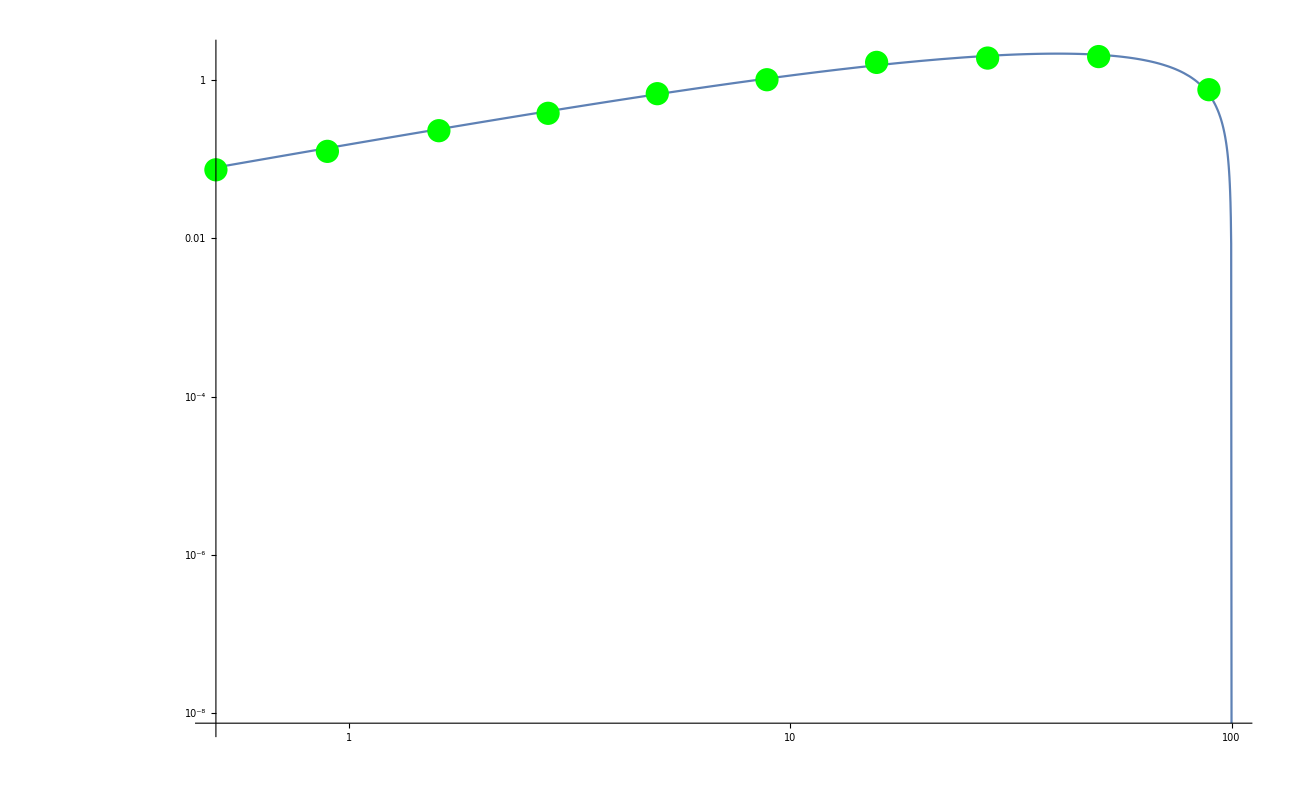

```mathematica
dNdx0a[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);(*Photon spectrum for one mediator decaying at rest to e^+e^-γ*)
dNdx1a[x1_,ϵ1_,ϵf_]:=(t1maxa=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1mina=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0a[x0,ϵf],{x0,t1mina,t1maxa}])(*boosted photon spectrum from two mediators*)
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1a[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA]
Show[LogLogPlot[En^2 dNdE1e[En,100.,0.005],{En,0.5,100.},PlotRange->All],ListLogLogPlot[outlist⟦3⟧,PlotStyle->Green]]
(*Show[LogLogPlot[x^2 dNdx0a[x,0.1],{x,0.001,1.},PlotRange->All],LogLogPlot[x^2 dNdx1a[x,0.001,0.1],{x,0.001,1.},PlotRange->All,PlotStyle->Green]]*)
```

```mathematica
outlist
```

{10.,0.001,{{0.5,0.0526697},{0.894427,0.0791692},{1.6,0.133686},{2.82843,0.193979},{5.,0.179322},{8.86002,0.0417297},{15.7,0.},{28.0179,0.},{50.,0.},{88.8819,0.},{158.,0.}}}

## Generating Functions

### Generate Escape Velocity

```mathematica
If[build==1,
Mtab=Table[{SSM⟦i,2⟧*SR,SSM⟦i,1⟧*SM},{i,2,Length[SSM]}];
Mi=Interpolation[Mtab,InterpolationOrder->1];
vetab= Table[{r,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,r}]-(Gconst Mi[SR])/SR))},{r,SR/100,SR,SR/100}];
vetab=Prepend[vetab,{0.0001,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,0.001}]-(Gconst Mi[SR])/SR))}];
Export["data/Escape.csv",vetab,"CSV"];]
```

### Generate fS

```mathematica
If[build==1,
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
(*normconstant=1/NIntegrate[fnonorm[√(x^2+y^2+z^2)],{x,0,vgal},{y,0,vgal},{z,0,vgal}]*)
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
Export["data/upint.csv",upint,"CSV"];
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
Export["data/f.csv",ftab,"CSV"];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
Export["data/fS.csv",fStab,"CSV"];]
```

## Generation Of Data

```mathematica
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
EN[i_]:=0.114/An⟦i⟧^(5/3);
Emin[mχ_,u_,r_]:=1/2 mχ u^2 1/c^2/.{c-> 3 10^8};
Emax[i_,mχ_,u_,r_]:=2 (mχ^2 mn⟦i⟧)/(mn⟦i⟧+mχ)^2(u^2+vei[r]^2)1/c^2/.{c-> 3 10^8};
xN[i_,ER_,mA_]:=(2mn⟦i⟧ ER + mA^2)/(2mn⟦i⟧ EN[i]);
expintegrand[i_,mχ_,mA_,u_,r_]:=(xNmax=xN[i,Emax[i,mχ,u,r],mA];
xNmin=xN[i,Emin[mχ,u,r],mA];
Exp[-xNmin]/xNmin+ExpIntegralEi[-xNmin]-Exp[-xNmax]/xNmax-ExpIntegralEi[-xNmax]);
uintegrand[u_]:=u fSi[u];
rintegrand[i_,r_]:=r^2 ndf⟦i⟧[r];
cNcap[i_,mχ_,mA_]:=NIntegrate[rintegrand[i,r]uintegrand[u]expintegrand[i,mχ,mA,u,r]HeavisideTheta[xN[i,Emax[i,mχ,u,r],mA]-xN[i,Emin[mχ,u,r],mA]],{r,0,SR},{u,0,upint},WorkingPrecision->5,MinRecursion->2,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
Ccap[mχ_,mA_,ϵ_,αχ_]:=32 π^3 ϵ^2 αχ α nχ Sum[zn⟦i⟧^2/(mn⟦i⟧EN[i])Exp[mA^2/(2mn⟦i⟧EN[i])]cNcap[i,mχ,mA],{i,1,Length[atomscut]}] ℏ^2 c^4/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8 }/.{α-> 1/137.,nχ-> ρχ/mχ};
σannvBorn[mχ_,mA_,αχ_]:=(π αχ^2)/mχ^2((1-mA^2/mχ^2)^(3/2))/((1-mA^2/(2 mχ^2))^2);
Som[a_,c_]:=π/a Sinh[2π a c]/(Cosh[2π a c]-Cos[2 π √(c-a^2 c^2)]);

Somav[mχ_,mA_,αχ_]:=(v0=5.1 10^-5 √(1000/mχ);
NIntegrate[(4π v^2)/((2π v0^2)^(3/2))Exp[-1/2 v^2/v0^2]Som[v/(2αχ),(6αχ mχ)/(π^2 mA)],{v,0,10v0},Method->{Automatic,"SymbolicProcessing"->0}])
Cann[mχ_,mA_,αχ_]:=Somav[mχ,mA,αχ]σannvBorn[mχ,mA,αχ](*1/GeV^2*)((GN mχ (*GeV*) ρS)/(3TS kB))^(3/2)ℏ^2/.{GN-> 6.67 10^-11(*m^3/(kg s^2)*),ρS-> 0.151  100^3(*kg/m^3*),TS-> 15.5 10^6(*kelvin*),kB-> 8.617333 10^-5 10^-9(*GeV kelvin^-1*)}/.{c-> 2.99792458 10^8(* m/s*)}/.{ℏ-> 6.582119 10^-22 0.001 (*GeV s*)}
τ[mχ_,mA_,ϵ_,αχ_]:=1/(√(Ccap[mχ,mA,ϵ,αχ]Cann[mχ,mA,αχ]));
τS=4.5 10^9 yr/.{yr->365 day}/.{day-> 24h}/.{h-> 3600};
τratio[mχ_,mA_,ϵ_,αχ_]:=τ[mχ,mA,ϵ,αχ]/τS

(*SIMPLIFIED MODEL BEGIN*)
(*From 1312.6408*)
Simpσi[mχ_,i_,σSI_,σSD_,mi_,A_,Z_]:=If[i==1,σSI+σSD,(mi^2 (mp+mχ)^2 A^2 σSI)/(mp^2 (mi+mχ)^2)(*(A^2 σSI (mi/mp)^2(mp+mχ)^2)/(mi+mχ)^2*)(*+(A^2 σSD (mp+mχ)^2)/(mi+mχ)^2*)](*m^2*);
Simprintegrand[r_,i_]:=4π r^2 ndf⟦i⟧[r];
Simpuintegrand[r_,u_]:=4π u(u^2+vei[r]^2)fSi[u];
Δmax[r_,u_,mχ_,mi_]:=(4 mi mχ)/(mχ + mi)^2;
Δmin[r_,u_,mχ_,mi_]:=u^2/(u^2+vei[r]^2);
Pri[r_,u_,mχ_,mi_]:=Max[0,(Δmax[r,u,mχ,mi]-Δmin[r,u,mχ,mi])/Δmax[r,u,mχ,mi]];
upintHS[mχ_,mNu_]:=((0.+8.439776214093713*^6 ) √mχ √mNu)/((mχ+mNu) √(9.-(36. mχ mNu)/(mχ+mNu)^2));
SimpcNcap[mχ_,i_,σSI_,σSD_]:=nχ Block[ {mNt,ZNt,ANt,ENt},
mNt=mn[[i]];
ZNt=zn[[i]];
ANt=An[[i]];
ENt=EN[i];
Simpσi[mχ,i,σSI,σSD,mNt,ANt,ZNt] NIntegrate[
Simprintegrand[r,i]Simpuintegrand[r,u]Pri[r,u,mχ,mNt],
{r,0,SR},{u,0,vgal(*0.5(*upint*)upintHS[mχ,mNt]*)},WorkingPrecision->4,Method-> {Automatic,"SymbolicProcessing"->0}]]/.{nχ-> ρχ/mχ};
SimpCcap[mχ_,σSI_,σSD_]:=Sum[SimpcNcap[mχ,i,σSI,σSD],{i,1,Length[atomscut]}];
(*SIMPLIFIED MODEL END*)



(*Results from 1305.1817, valid for 0.1-10GeV mχ*)
CGB[mχ_,σSI_,σSD_]:=3.57 Exp[1.34(Log[20./(mχ (*GeV*))])^0.86]((σSD(*m^2*) 100^2(*cm^2/m^2*))/(10^-40(*cm^2*))) 10^23+5.27 Exp[3.73 10^-2(Log[20./(mχ (*GeV*))])^2.23]((σSI(*m^2*) 100^2(*cm^2/m^2*))/(10^-40(*cm^2*)))1 10^25;



(*Results from 1104.0679*)
SKvS=220 10^3(*velocity of sun, m/s*);
SKuintegrand[u_]:=c^2/(√π SKvS^2)(Exp[(-(u-SKvS)^2)/SKvS^2]-Exp[(-(u+SKvS)^2)/SKvS^2])/.{c-> 2.99792458 10^8 (*m/s*)}
SKFER2[i_,SKER_]:=Exp[-SKER(* GeV*)/SKEi]/.{SKEi-> (3 ℏ^2 c^2)/(2mn⟦i⟧(*GeV*) SKRi^2)}/.{SKRi-> (0.9 An⟦i⟧^(1/3)+0.3)10^-15(*m*)}/.{ℏ-> 6.582119 10^-22 0.001 (*GeV s*)}/.{c-> 2.99792458 10^8(* m/s*)}
SKERmin[mχ_,u_]:=1/2 mχ u^2/c^2/.{c-> 2.99792458 10^8 (*m/s*)}
SKERmax[i_,mχ_,u_,r_?NumericQ]:=(2 μi^2)/mn⟦i⟧(u^2+vei[r]^2)/c^2/.{μi-> (mχ mn⟦i⟧)/(mχ+mn⟦i⟧)}/.{c-> 2.99792458 10^8 (*m/s*)}
SKdCidV[i_,mχ_,σi_,r_?NumericQ]:=(ρχ mn⟦i⟧ndf⟦i⟧[r])/(2mχ μi^2)σi NIntegrate[If[SKERmax[i,mχ,u,r]-SKERmin[mχ,u]>0,SKuintegrand[u]SKFER2[i,SKER],0],{u,0,vgal},{SKER,SKERmin[mχ,u],SKERmax[i,mχ,u,r]},WorkingPrecision-> 3,Method-> {Automatic,"SymbolicProcessing"->0}]/.{μi-> (mχ mn⟦i⟧)/(mχ+mn⟦i⟧)}

GeV/m^3 GeV 1/m^3 1/GeV 1/GeV^2 m^2 m/s GeV
SKCS[mχ_,σp_]:=Sum[NIntegrate[4π r^2 SKdCidV[i,mχ,σp zn⟦i⟧^2((mχ mn⟦i⟧)/(mχ+mn⟦i⟧))^2((mχ+mp)/(mχ mp))^2,r],{r,0,SR},WorkingPrecision->3,Method-> {Automatic,"SymbolicProcessing"->0}],{i,1,Length[mn]}]
m^2 1/(m^3 s)m

ti=1;
tmχ=100000;
tmA=5.;
tϵ= 10.^-8;
tαχ=0.024/1000 tmχ;
tu=0.1vgal;
tr=0.5SR;
tσ=10^-44(*m^2*);


microrun[tαχ,tmA,tmχ,tϵ]
tσ=%[[1]]
(*SKdCidV[ti,tmχ,10^-40,tr]
*)AbsoluteTiming[SKCS[tmχ,tσ]]
(*CGB[tmχ,tσ,0]
SimpCcap[tmχ,tσ,0.]*)
```

1/(m^3 s)

1/s

{5.181×10^-51,5.10516×10^12}

5.181×10^-51

{4.08333,4.28×10^12}

```mathematica
table1=Table[{10^lmχ,SimpCcap[10^lmχ,tσ,0]},{lmχ,-1,2,0.05}];

table2=Table[{10^lmχ,CGB[10^lmχ,tσ,0]},{lmχ,-1,1,0.1}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
table3=Table[{10^lmχ,SimpCcap[10^lmχ,10^-40,0]},{lmχ,-2,3,0.05}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
table4=Table[{10^lmχ,SimpCcap[10^lmχ,10^-44,0]},{lmχ,-2,4,0.25}];
```

```mathematica
table5=Table[{10^lmχ,SKCS[10^lmχ,10^-44]},{lmχ,0,4,0.1}];
```

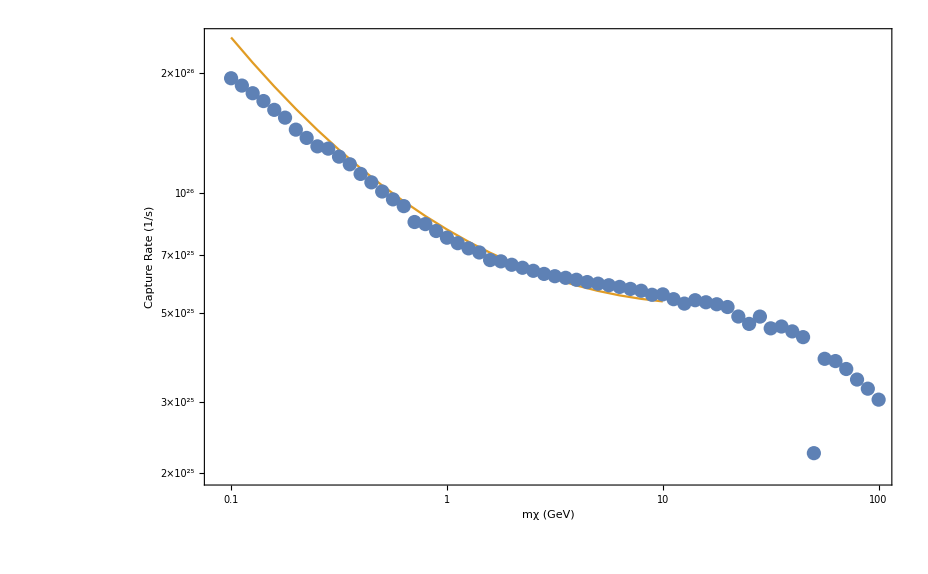

```mathematica
ListLogLogPlot[{table1,table2},Frame->True,FrameStyle->Black,FrameLabel->{"mχ (GeV)","Capture Rate (1/s)"},LabelStyle->30,Joined->{False,True}]
```

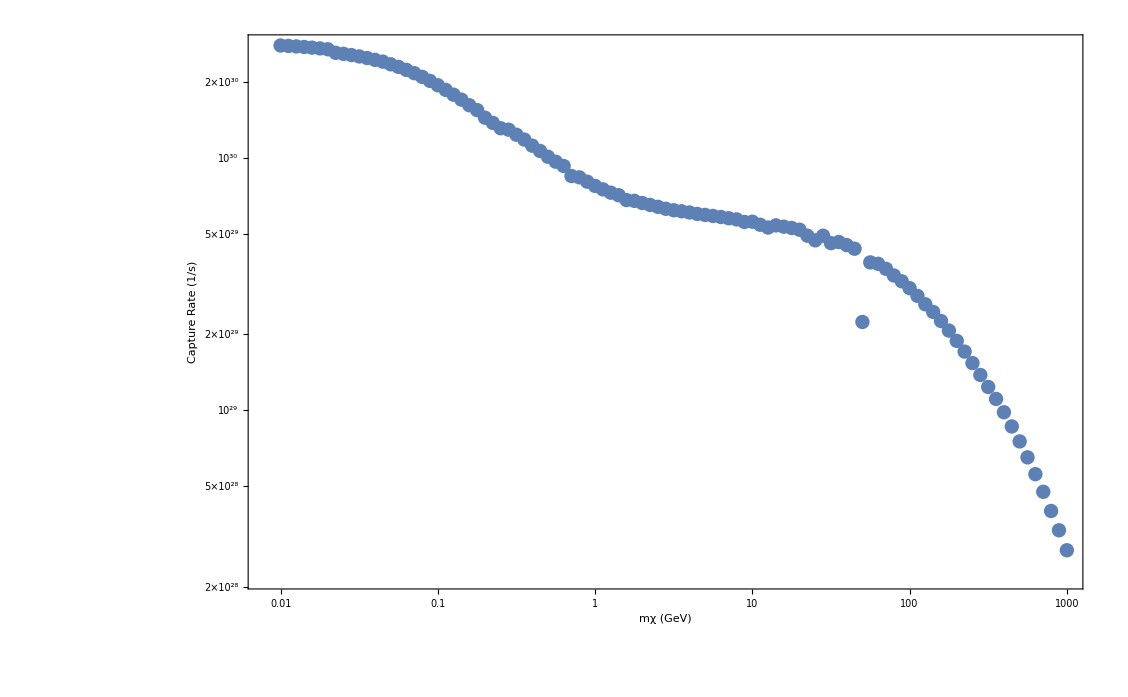

```mathematica
ListLogLogPlot[table3,Frame->True,FrameStyle->Black,FrameLabel->{"mχ (GeV)","Capture Rate (1/s)"},LabelStyle->30]
```

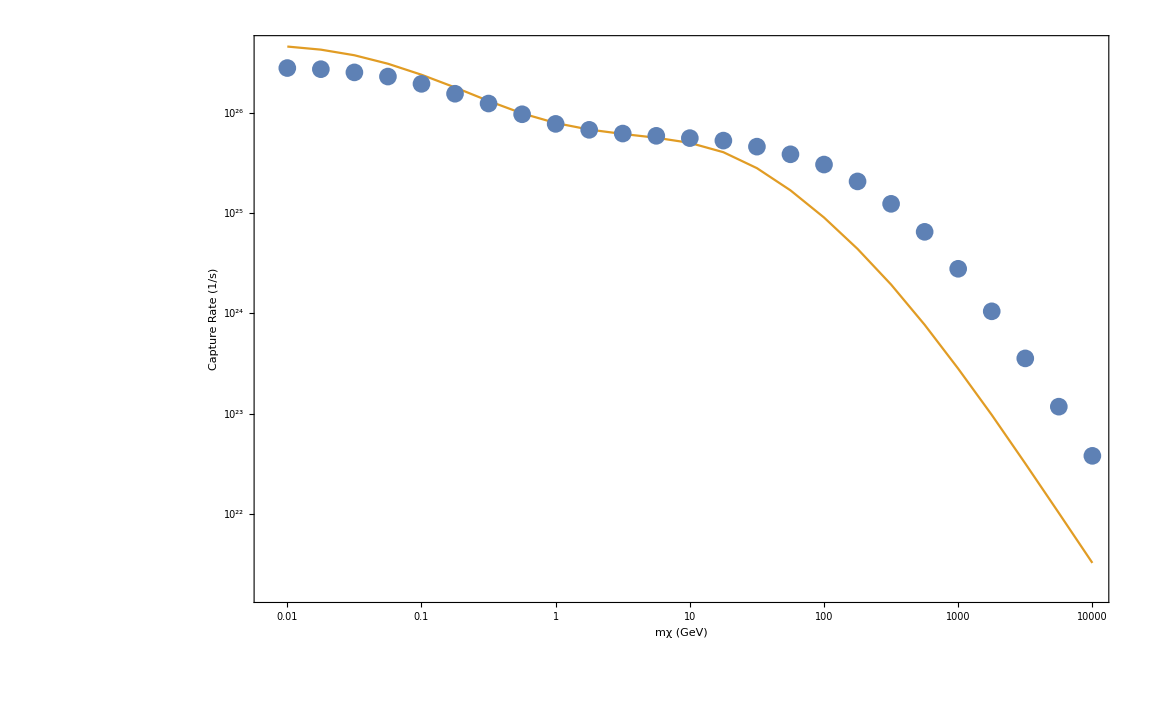

```mathematica
ListLogLogPlot[{table4,table5},Frame->True,FrameStyle->Black,FrameLabel->{"mχ (GeV)","Capture Rate (1/s)"},LabelStyle->30,Joined->{False,True},PlotRange->All]
```

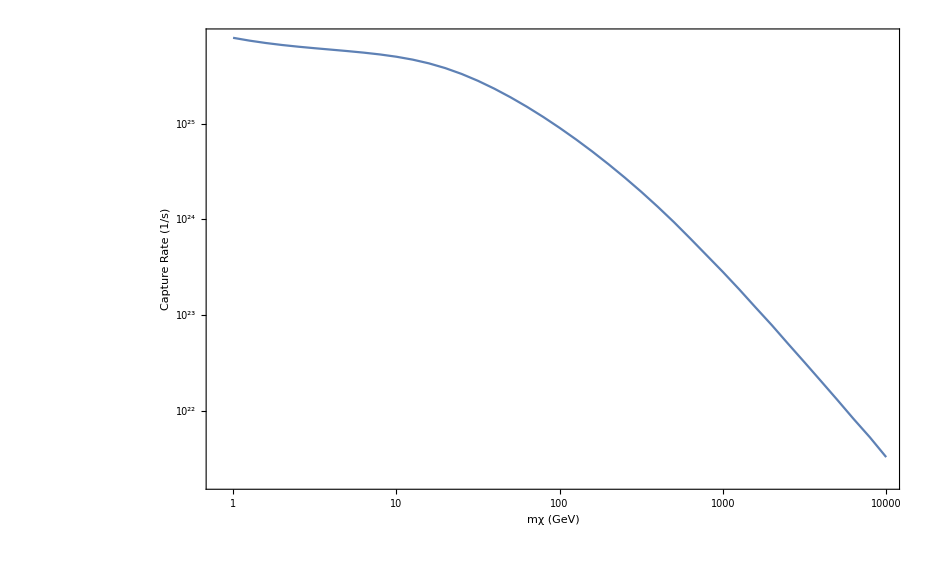

```mathematica
ListLogLogPlot[table5,Frame->True,FrameStyle->Black,FrameLabel->{"mχ (GeV)","Capture Rate (1/s)"},LabelStyle->30,Joined->True,PlotRange->All]
```

```mathematica
LogLogPlot[{CGB[mχ,tσ,0],SimpCcap[mχ,tσ,0]},{mχ,0.1,10},PlotRange->{Automatic,{10^24,10^26.5}},Frame->True,FrameStyle->Black,FrameLabel->{"mχ (GeV)","Capture Rate (1/s)"},LabelStyle->30]
```

$Aborted

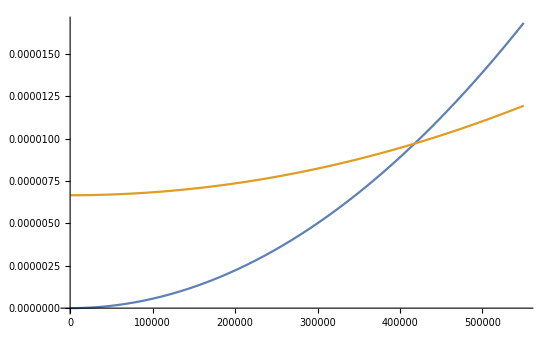

```mathematica
Plot[{SKERmin[tmχ,u],SKERmax[ti,tmχ,u,SR]},{u,0,vgal}]
```

```mathematica
mχi=1;
mχf=5;
mχstep=0.05;
DPtab=Table[{10^lmχ,Ccap[10^lmχ,tmA,tϵ,0.024/1000 10^lmχ]},{lmχ,mχi,mχf,mχstep}]
microtabpre=Table[Join[{10^lmχ},microrun[0.024/1000 10^lmχ,tmA,10^lmχ,tϵ]],{lmχ,mχi,mχf,mχstep}];
microtab=Table[{microtabpre⟦i,1⟧,microtabpre⟦i,3⟧},{i,1,Length[microtabpre]}]
Simptab=Table[{microtabpre⟦i,1⟧,SimpCcap[microtabpre⟦i,1⟧,microtabpre⟦i,2⟧,0.]},{i,1,Length[microtab]}]
```

```mathematica
mAi=-3;
mAf=1;
mAstep=0.05;
DPtab=Table[{10^lmA,Ccap[tmχ,10^lmA,tϵ,0.024/1000 tmχ]},{lmA,mAi,mAf,mAstep}]
microtabpre=Table[Join[{10^lmA},microrun[0.024/1000 tmχ,lmA,tmχ,tϵ]],{lmA,mAi,mAf,mAstep}];
microtab=Table[{microtabpre⟦i,1⟧,microtabpre⟦i,3⟧},{i,1,Length[microtabpre]}]
Simptab=Table[{microtabpre⟦i,1⟧,SimpCcap[microtabpre⟦i,1⟧,microtabpre⟦i,2⟧,0.]},{i,1,Length[microtab]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.001,2.23215×10^22},{0.00112202,2.05753×10^22},{0.00125893,1.90754×10^22},{0.00141254,1.76464×10^22},{0.00158489,1.62627×10^22},{0.00177828,1.47456×10^22},{0.00199526,1.3372×10^22},{0.00223872,1.20449×10^22},{0.00251189,1.07677×10^22},{0.00281838,9.52811×10^21},{0.00316228,8.63727×10^21},{0.00354813,7.37415×10^21},{0.00398107,6.37428×10^21},{0.00446684,5.44939×10^21},{0.00501187,4.62671×10^21},{0.00562341,3.89495×10^21},{0.00630957,3.2637×10^21},{0.00707946,2.77865×10^21},{0.00794328,2.23108×10^21},{0.00891251,1.84667×10^21},{0.01,1.50325×10^21},{0.0112202,1.24892×10^21},{0.0125893,1.02374×10^21},{0.0141254,8.39129×10^20},{0.0158489,6.54202×10^20},{0.0177828,5.49795×10^20},{0.0199526,4.40544×10^20},{0.0223872,3.49552×10^20},{0.0251189,2.13896×10^20},{0.0281838,2.15045×10^20},{0.0316228,1.66805×10^20},{0.0354813,1.28255×10^20},{0.0398107,9.82477×10^19},{0.0446684,7.48996×10^19},{0.0501187,5.69627×10^19},{0.0562341,4.3359×10^19},{0.0630957,3.28969×10^19},{0.0707946,2.48109×10^19},{0.0794328,1.87143×10^19},{0.0891251,1.37675×10^19},{0.1,1.0368×10^19},{0.112202,7.65385×10^18},{0.125893,5.57824×10^18},{0.141254,4.01797×10^18},{0.158489,2.85639×10^18},{0.177828,1.98206×10^18},{0.199526,1.40038×10^18},{0.223872,9.60442×10^17},{0.251189,6.54746×10^17},{0.281838,4.3592×10^17},{0.316228,2.90808×10^17},{0.354813,1.91923×10^17},{0.398107,1.27457×10^17},{0.446684,8.31385×10^16},{0.501187,5.40204×10^16},{0.562341,3.48787×10^16},{0.630957,2.242×10^16},{0.707946,1.4362×10^16},{0.794328,9.1739×10^15},{0.891251,5.84644×10^15},{1.,3.71756×10^15},{1.12202,2.35885×10^15},{1.25893,1.42817×10^15},{1.41254,8.98094×10^14},{1.58489,5.37209×10^14},{1.77828,3.20811×10^14},{1.99526,1.59442×10^14},{2.23872,1.00796×10^14},{2.51189,6.36963×10^13},{2.81838,4.02391×10^13},{3.16228,2.5809×10^13},{3.54813,1.31516×10^13},{3.98107,7.2942×10^12},{4.46684,2.34184×10^12},{5.01187,7.89456×10^11},{5.62341,3.52203×10^11},{6.30957,2.22227×10^11},{7.07946,1.40216×10^11},{7.94328,5.84346×10^9},{8.91251,3.62462×10^9},{10.,2.28698×10^9}}

{{0.001,3.93916×10^13},{0.00112202,4.21309×10^13},{0.00125893,4.51125×10^13},{0.00141254,4.83626×10^13},{0.00158489,5.19107×10^13},{0.00177828,5.57902×10^13},{0.00199526,6.00391×10^13},{0.00223872,6.47002×10^13},{0.00251189,6.98225×10^13},{0.00281838,7.5462×10^13},{0.00316228,8.16825×10^13},{0.00354813,8.85574×10^13},{0.00398107,9.6171×10^13},{0.00446684,1.04621×10^14},{0.00501187,1.14019×10^14},{0.00562341,1.24497×10^14},{0.00630957,1.36207×10^14},{0.00707946,1.49326×10^14},{0.00794328,1.64064×10^14},{0.00891251,1.80665×10^14},{0.01,1.9942×10^14},{0.0112202,2.20674×10^14},{0.0125893,2.44836×10^14},{0.0141254,2.72397×10^14},{0.0158489,3.03948×10^14},{0.0177828,3.40202×10^14},{0.0199526,3.82026×10^14},{0.0223872,4.3048×10^14},{0.0251189,4.86866×10^14},{0.0281838,5.52793×10^14},{0.0316228,6.30266×10^14},{0.0354813,7.218×10^14},{0.0398107,8.30571×10^14},{0.0446684,9.60625×10^14},{0.0501187,1.11716×10^15},{0.0562341,1.30692×10^15},{0.0630957,1.53874×10^15},{0.0707946,1.82431×10^15},{0.0794328,2.17931×10^15},{0.0891251,2.62502×10^15},{0.1,3.19072×10^15},{0.112202,3.91737×10^15},{0.125893,4.86317×10^15},{0.141254,6.11242×10^15},{0.158489,7.78985×10^15},{0.177828,1.00843×10^16},{0.199526,1.32891×10^16},{0.223872,1.78746×10^16},{0.251189,2.46198×10^16},{0.281838,3.48689×10^16},{0.316228,5.10516×10^16},{0.354813,7.78106×10^16},{0.398107,1.24638×10^17},{0.446684,2.12626×10^17},{0.501187,3.93916×10^17},{0.562341,8.16825×10^17},{0.630957,1.9942×10^18},{0.707946,6.30266×10^18},{0.794328,3.19072×10^19},{0.891251,5.10516×10^20},{1.,6.47155×10^26},{1.12202,5.10516×10^20},{1.25893,3.19072×10^19},{1.41254,6.30266×10^18},{1.58489,1.9942×10^18},{1.77828,8.16825×10^17},{1.99526,3.93916×10^17},{2.23872,2.12626×10^17},{2.51189,1.24638×10^17},{2.81838,7.78106×10^16},{3.16228,5.10516×10^16},{3.54813,3.48689×10^16},{3.98107,2.46198×10^16},{4.46684,1.78746×10^16},{5.01187,1.32891×10^16},{5.62341,1.00843×10^16},{6.30957,7.78985×10^15},{7.07946,6.11242×10^15},{7.94328,4.86317×10^15},{8.91251,3.91737×10^15},{10.,3.19072×10^15}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.001,8.60031×10^20},{0.00112202,9.19407×10^20},{0.00125893,9.83828×10^20},{0.00141254,1.05413×10^21},{0.00158489,1.1307×10^21},{0.00177828,1.21436×10^21},{0.00199526,1.3057×10^21},{0.00223872,1.40574×10^21},{0.00251189,1.51545×10^21},{0.00281838,1.63602×10^21},{0.00316228,1.7684×10^21},{0.00354813,1.91435×10^21},{0.00398107,2.07517×10^21},{0.00446684,2.25358×10^21},{0.00501187,2.4497×10^21},{0.00562341,2.66949×10^21},{0.00630957,2.91033×10^21},{0.00707946,3.18002×10^21},{0.00794328,3.48191×10^21},{0.00891251,3.81913×10^21},{0.01,4.19448×10^21},{0.0112202,4.61657×10^21},{0.0125893,5.08928×10^21},{0.0141254,5.62191×10^21},{0.0158489,6.2207×10^21},{0.0177828,6.89668×10^21},{0.0199526,7.65905×10^21},{0.0223872,8.25256×10^21},{0.0251189,9.20592×10^21},{0.0281838,1.02886×10^22},{0.0316228,1.15187×10^22},{0.0354813,1.29183×10^22},{0.0398107,1.45112×10^22},{0.0446684,1.63877×10^22},{0.0501187,1.84607×10^22},{0.0562341,2.08349×10^22},{0.0630957,2.35727×10^22},{0.0707946,2.66871×10^22},{0.0794328,3.02971×10^22},{0.0891251,3.44642×10^22},{0.1,3.93441×10^22},{0.112202,4.5141×10^22},{0.125893,5.21375×10^22},{0.141254,6.07723×10^22},{0.158489,7.10438×10^22},{0.177828,8.50945×10^22},{0.199526,1.02971×10^23},{0.223872,1.28195×10^23},{0.251189,1.63488×10^23},{0.281838,2.17177×10^23},{0.316228,2.94765×10^23},{0.354813,4.19983×10^23},{0.398107,6.17059×10^23},{0.446684,9.79995×10^23},{0.501187,1.67625×10^24},{0.562341,3.25288×10^24},{0.630957,7.57589×10^24},{0.707946,2.11328×10^25},{0.794328,1.02064×10^26},{0.891251,1.53236×10^27},{1.,1.82263×10^33},{1.12202,1.36099×10^27},{1.25893,8.0386×10^25},{1.41254,1.51482×10^25},{1.58489,4.51325×10^24},{1.77828,1.78224×10^24},{1.99526,8.26056×10^23},{2.23872,4.28767×10^23},{2.51189,2.42841×10^23},{2.81838,1.45688×10^23},{3.16228,9.2821×10^22},{3.54813,6.18316×10^22},{3.98107,4.28633×10^22},{4.46684,3.00006×10^22},{5.01187,2.17968×10^22},{5.62341,1.6173×10^22},{6.30957,1.22455×10^22},{7.07946,9.39089×10^21},{7.94328,7.31654×10^21},{8.91251,5.70117×10^21},{10.,4.60638×10^21}}

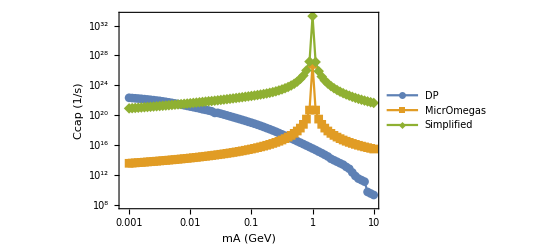

```mathematica
ListLogLogPlot[{DPtab,microtab,Simptab},Frame->True,FrameStyle->Black,LabelStyle->30,Joined->True,PlotMarkers->Automatic,FrameLabel->{"mA (GeV)"," Ccap (1/s)"},PlotLegends->{"DP","MicrOmegas","Simplified"}]
```

```mathematica
mAi=1;
mAf=3;
mAstep=0.05;
DPtab=Table[{10^lmχ,Ccap[10^lmχ,tmA,tϵ,tαχ]},{lmχ,mχi,mχf,mχstep}];
microtabpre=Table[Join[{10^lmχ},microrun[tαχ,tmA,10^lmχ,tϵ]],{lmχ,mχi,mχf,mχstep}];
microtab=Table[{microtabpre⟦i,1⟧,microtabpre⟦i,3⟧},{i,1,Length[microtabpre]}];
Simptab=Table[{microtabpre⟦i,1⟧,SimpCcap[microtabpre⟦i,1⟧,microtabpre⟦i,2⟧,0.]},{i,1,Length[microtab]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
ListLogLogPlot[{DPtab,microtab,Simptab},Frame->True,FrameStyle->Black,LabelStyle->30,Joined->True,PlotMarkers->Automatic,FrameLabel->{"mχ (GeV)"," Ccap (1/s)"},PlotLegends->{"DP","MicrOmegas","Simplified"}]
```

```mathematica
AbsoluteTiming[tabepm8mx100=Table[{lmA,τratio[100.,10.^lmA,10.^-8,0.035/1000 100.]},{lmA,-3.1,0.1,0.01}];]
Export["tabepm8mx100.csv",tabepm8mx100,"CSV"]
```

```mathematica
AbsoluteTiming[tabepm8mx1000=Table[{lmA,τratio[1000.,10.^lmA,10.^-8,0.035/1000 1000.]},{lmA,-3.1,0.1,0.01}];]
Export["tabepm8mx1000.csv",tabepm8mx1000,"CSV"]
```

```mathematica
AbsoluteTiming[tabepm8mx10000=Table[{lmA,τratio[10000.,10.^lmA,10.^-8,0.035/1000 10000.]},{lmA,-3.1,0.1,0.01}];]
Export["tabepm8mx10000.csv",tabepm8mx10000,"CSV"]
```

```mathematica
tabepm8=Import["tabepm8mx100.csv"];
plottab=Flatten[Table[{tabepm8⟦i,1⟧,lϵ,10^-8/10^lϵ tabepm8⟦i,2⟧},{lϵ,-12,-6.9,0.01},{i,1,Length[tabepm8]}],1];
thickness=0.005;

cp=ListContourPlot[plottab,Contours-> {10.^-6,10.^-4,10.^-2,10.^0,10.^2},ContourShading->None,ContourStyle-> {Directive[Thickness[thickness],Red],Directive[Thickness[thickness],Orange],Directive[Thickness[thickness],Brown],Directive[Thickness[thickness],Green],Directive[Thickness[thickness],Blue]},InterpolationOrder->1,PlotRange->All,Frame->True];
epilog={Style[Text["m_χ = 100 GeV",{-2.5,-7.2}],20,Black],Style[Text["10^-4",{-2.5,-8}],20,Orange],Style[Text["10^-2",{-2.5,-10}],20,Brown],Style[Text["10^0",{-1.3,-10.5}],20,Green],Style[Text["10^-2",{-0.6,-11}],20,Blue]};
Show[cp,PlotRange-> {{-2.95,-0.05},{-11.4,-7.1}},Frame->True,FrameLabel-> {"Dark Photon Mass log(m_A')","Mixing Parameter log(ϵ)"},FrameStyle->Black,LabelStyle->20,Epilog-> epilog,ImageSize-> 750]
```

```mathematica
tabepm8=Import["tabepm8mx1000.csv"];
plottab=Flatten[Table[{tabepm8⟦i,1⟧,lϵ,10^-8/10^lϵ tabepm8⟦i,2⟧},{lϵ,-12,-6.9,0.01},{i,1,Length[tabepm8]}],1];
thickness=0.005;

cp=ListContourPlot[plottab,Contours-> {10.^-6,10.^-4,10.^-2,10.^0,10.^2},ContourShading->None,ContourStyle-> {Directive[Thickness[thickness],Red],Directive[Thickness[thickness],Orange],Directive[Thickness[thickness],Brown],Directive[Thickness[thickness],Green],Directive[Thickness[thickness],Blue]},InterpolationOrder->1,PlotRange->All,Frame->True];
epilog={Style[Text["m_χ = 1 TeV",{-2.5,-8.1}],20,Black],Style[Text["10^-6",{-2.5,-7.3}],20,Red],Style[Text["10^-4",{-2.5,-8.95}],20,Orange],Style[Text["10^-2",{-2.5,-11}],20,Brown],Style[Text["10^0",{-0.7,-10.8}],20,Green],Style[Text["10^-2",{-0.15,-11.3}],20,Blue]};
Show[cp,PlotRange-> {{-2.95,-0.05},{-11.4,-7.1}},Frame->True,FrameLabel-> {"Dark Photon Mass log(m_A')","Mixing Parameter log(ϵ)"},FrameStyle->Black,LabelStyle->20,Epilog-> epilog,ImageSize-> 750]
```

```mathematica
tabepm8=Import["tabepm8mx10000.csv"];
plottab=Flatten[Table[{tabepm8⟦i,1⟧,lϵ,10^-8/10^lϵ tabepm8⟦i,2⟧},{lϵ,-12,-6.9,0.01},{i,1,Length[tabepm8]}],1];
thickness=0.005;

cp=ListContourPlot[plottab,Contours-> {10.^-6,10.^-4,10.^-2,10.^0,10.^2},ContourShading->None,ContourStyle-> {Directive[Thickness[thickness],Red],Directive[Thickness[thickness],Orange],Directive[Thickness[thickness],Brown],Directive[Thickness[thickness],Green],Directive[Thickness[thickness],Blue]},InterpolationOrder->1,PlotRange->All,Frame->True];
epilog={Style[Text["m_χ = 10 TeV",{-2.5,-7.2}],20,Black],Style[Text["10^-6",{-2.5,-8}],20,Red],Style[Text["10^-4",{-2.5,-10}],20,Orange],Style[Text["10^-2",{-1.4,-11}],20,Brown],Style[Text["10^0",{-0.3,-11}],20,Green]};
Show[cp,PlotRange-> {{-2.95,-0.05},{-11.4,-7.1}},Frame->True,FrameLabel-> {"Dark Photon Mass log(m_A')","Mixing Parameter log(ϵ)"},FrameStyle->Black,LabelStyle->20,Epilog-> epilog,ImageSize-> 750]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

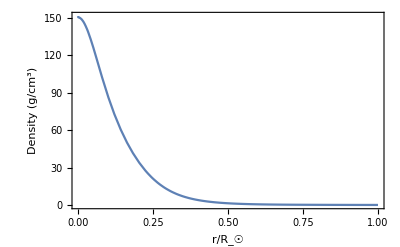

```mathematica
plotdensity=Interpolation[Table[{SSM⟦i,2⟧,SSM⟦i,4⟧},{i,2,Length[SSM]}]]
Plot[plotdensity[r],{r,0,1},PlotRange->All,Frame->True,FrameStyle->Black,FrameLabel->{"r/R_☉","Density (g/cm^3)"}]
```

InterpolatingFunction::dmval: Input value {14217.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

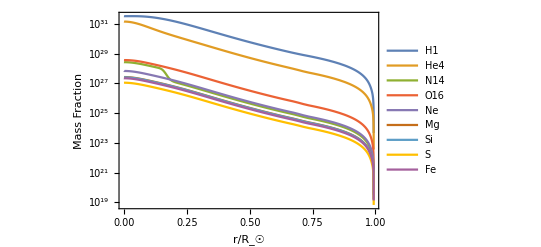

```mathematica
LogPlot[{InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r],InterpolatingFunction[…][6.9598*^8 r]},{r,0,1},PlotRange->All,PlotLegends->atomscut,Frame->True,FrameStyle->Black,FrameLabel-> {"r/R_☉","Mass Fraction"}]
```

```mathematica
Table[ndf⟦i⟧[r*SR],{i,1,Length[ndf]}]
```

{InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r],InterpolatingFunction[…][6.9598×10^8 r]}

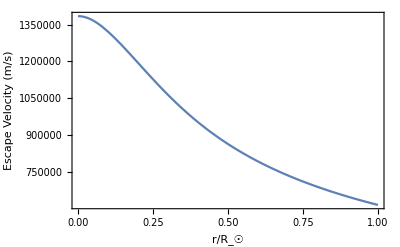

```mathematica
Plot[vei[r*SR],{r,0,1},Frame->True,FrameStyle->Black,FrameLabel-> {"r/R_☉","Escape Velocity (m/s)"}]
```